#### Variance

```mathematica
ClearAll["Global`*"]
fs=FullSimplify;
ft=Flatten;
A[v_]:=Seq[v]

Seq[v_]:=(d + α + U f)/(β0-(n v)/2)

paramsall = {β0 -> 4, n -> 2,b -> 3, d -> 1, α -> 1,f->0.4};
nnn=n/.paramsall
lam=λ/.paramsall
```

2

λ

```mathematica
solVw=Solve[Vw == Sqrt[(U (1-f)λ)/A[Vw]], Vw];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
solVw=Solve[Vw == Sqrt[(U (1-f)λ)/A[Vw]], Vw];
solVk=Solve[Vk== Sqrt[(U (1-f)λ)/A[Vk] - (3 U (1-f)λ^2)/(8 Vk A[Vk])], Vk][[1]] ;
solVk2=Solve[Vk== Sqrt[(U (1-f)λ)/A[Vk] - (3 U (1-f)λ^2)/(8 Vk A[Vk])], Vk][[2]] ;
solVk3=Solve[Vk== Sqrt[(U (1-f)λ)/A[Vk] - (3 U (1-f)λ^2)/(8 Vk A[Vk])], Vk][[3]] ;
solVhc=Solve[Vhc==(U (1-f)2)/(n A[Vhc]), Vhc];
solVhc3=Solve[Vhc3==(U (1-f)2)/(n A[Vhc3])-(2Pi)/λ((U(1-f))/(n A[Vhc3]))^2 , Vhc3][[1]];


Solve[(Vw/.solVw//First)==(Vhc/.solVhc//First),λ]//ft//First
limiteV=ListPlot[{{λ/.%/.paramsall/.U->4,-10},{λ/.%/.paramsall/.U->4,30}}, Joined->True, PlotStyle->Directive[Opacity[0.5,Black], Thickness@0.003]];



rec1=Graphics[{Opacity[0.05,Orange],Rectangle[{-10,-100},{λ/.%%/.paramsall/.U->4,100}]}];
rec2=Graphics[{Opacity[0.05,Cyan],Rectangle[{λ/.%%%/.paramsall/.U->4,-100},{100,100}]}];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

λ→-(4 (-1+f) U β0)/(n^2 (d+U+α))

```mathematica
Vw[l_,UU_]:=Vw/.solVw/.λ->l /.U-> UU


Vk[l_,UU_]:=Vk/.solVk/.λ->l /.U-> UU
Vk2[l_,UU_]:=Vk/.solVk2/.λ->l /.U-> UU
Vk3[l_,UU_]:=Vk/.solVk3/.λ->l /.U-> UU

Vhc[l_,UU_]:=Vhc/.solVhc/.λ->l /.U-> UU

Vhc2[l_,UU_]:=Vhc2/.solVhc2/.λ->l /.U-> UU

Vhc3[l_,UU_]:=Vhc3/.solVhc3/.λ->l /.U-> UU


VF[l_,UU_]:= Vw (1- l Vw (3/(16 UU)-19/16))/.solVw/.λ->l /.U-> UU
```

```mathematica
NSolve[Vk[λ,4] == (9/16)*λ/.paramsall,λ]
λ/.%//ft;
limiteVk=ListPlot[{{First[%],-10},{First[%],30}}, Joined->True, PlotStyle-> Directive[Opacity[0.5,Black],Dashed, Thickness@0.003]];


NSolve[ λ== (256 (1-f)U)/(243A[Vk[λ,4]])/.paramsall/.U->4,{λ}]
```

{{λ→2.01377}}

{{λ→2.01377},{λ→2.01377}}

#### Regarde le max de lambda dans le graph ci dessous (2.03) et la limite calculée ci dessus (2.013)

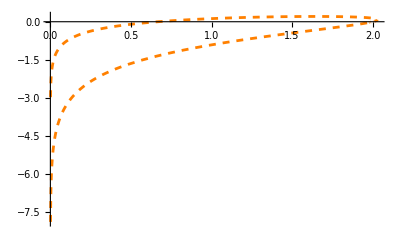

```mathematica
pVk=Plot[Evaluate[Log[Vk[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}, PlotRange->All];
pVk2=Plot[Evaluate[Log[Vk2[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}, PlotRange->All]; (*solution dans les complexes*)
pVk3=Plot[Evaluate[Log[Vk3[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}, PlotRange->All];


Show[pVk,pVk2,pVk3]
```

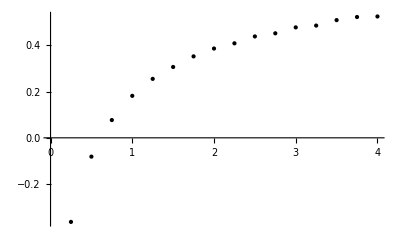

Sequence[]

```mathematica
If[nnn==2,
list1=Range[0.25,4,0.25];
list2={-0.36396721,-0.0814507, 0.07691702, 0.18174326, 0.2551976 ,0.30667453,0.35257165, 0.3865632 ,0.40909379, 0.43895551 ,0.45245938, 0.47811273,
0.48593847, 0.50952384, 0.52298491, 0.52537761};
popoints=ListPlot[Transpose[{Reverse[list1],Reverse[list2]}],PlotStyle->{Black,PointSize/@{Medium}}],
Unevaluated[Sequence[]]]



If[nnn==1,
list1=Range[0,6.5,0.5];
list2={-1.2120904255456937,-1.3409701088577037,-1.506757766698122,-1.715302739437194,-2.127033463651063,-2.421834985375469,-2.7389108893313625,-3.05356645116044,-3.3725813027308256,-3.7424950612500965,-4.125549615569775,-4.535523590858643,-4.969604264319412,-5.423603788640402};
popoints=ListPlot[Transpose[{Reverse[list1],Reverse[list2]}],PlotStyle->{Black,PointSize/@{Large}}],
Unevaluated[Sequence[]]]
```

```mathematica
popoints
```

-Graphics-

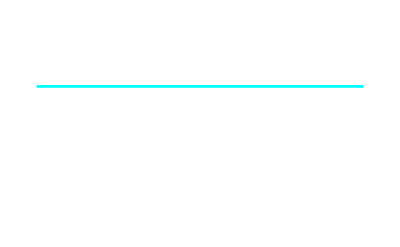

ReplaceAll::reps: {solVhc2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

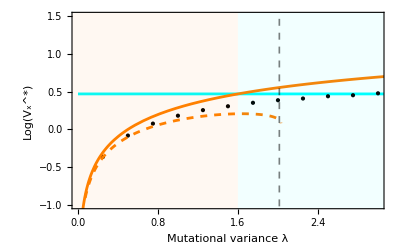

/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_lambda_variance_n2.pdf

```mathematica
pVw=Plot[Evaluate[Log[Vw[λ,4]]/.paramsall][[2]],{λ,0.001,4}, PlotStyle->Orange, PlotRange->All];
pVk=Plot[Evaluate[Log[Vk[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}];
pVk2=Plot[Evaluate[Log[Vk2[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}, PlotRange->All];
pVk3=Plot[Evaluate[Log[Vk3[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed, Orange}];
pVF=Plot[Evaluate[Log[VF[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dotted,Orange}];

Show[pVk,pVk3];
pVhc=Plot[Evaluate[Log[Vhc[λ,4]]/.paramsall],{λ,0.001,4},PlotRange->{All,{-5,3}}, PlotStyle->Cyan, Axes->False]
pVhc2=Plot[Evaluate[Log[Vhc2[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed,Gray}];
pVhc3=Plot[Evaluate[Log[Vhc3[λ,4]]/.paramsall],{λ,0.001,4}, PlotStyle->{Dashed,Cyan}];
Show[pVhc,popoints,pVw,pVk,rec1,rec2,limiteVk, PlotRange->{{0.001,3}, {-1,1.5}} , Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Mutational variance λ",13],Style["Log(V_x^*)",13]}, Axis->False]





Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_lambda_variance_n"<>ToString[nnn]<>".pdf",%, ImageResolution->300, ImageSize->600]
```

### S = Seq

```mathematica
paramsall
```

{β0→4,n→2,b→3,d→1,α→1,f→0.4}

{Vw→√(-((-1+f) U λ)/seq)}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{U→(-8 d f-8 f α+(8 b f β0)/d+(b^2 n^2 λ)/(d^2 seq)-(b^2 f n^2 λ)/(d^2 seq)-(b √(-1+f) n √λ √(16 d^3 f seq+16 d^2 f seq α-16 b d f seq β0-b^2 n^2 λ+b^2 f n^2 λ))/(d^2 seq))/(8 f^2)},{U→(-8 d f-8 f α+(8 b f β0)/d+(b^2 n^2 λ)/(d^2 seq)-(b^2 f n^2 λ)/(d^2 seq)+(b √(-1+f) n √λ √(16 d^3 f seq+16 d^2 f seq α-16 b d f seq β0-b^2 n^2 λ+b^2 f n^2 λ))/(d^2 seq))/(8 f^2)}}

(-8 d f-8 f α+(8 b f β0)/d+(b n^2 λ)/d-(b f n^2 λ)/d-(√(-1+f) n √λ √(16 b d^2 f+16 b d f α-16 b^2 f β0-b^2 n^2 λ+b^2 f n^2 λ))/d)/(8 f^2)

(-8 d f-8 f α+(8 b f β0)/d+(b n^2 λ)/d-(b f n^2 λ)/d+(√(-1+f) n √λ √(16 b d^2 f+16 b d f α-16 b^2 f β0-b^2 n^2 λ+b^2 f n^2 λ))/d)/(8 f^2)

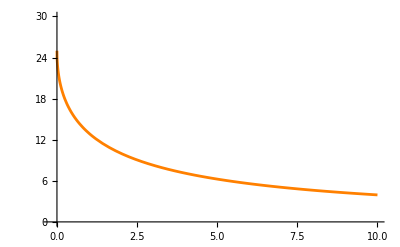

```mathematica
A[v_]:=seq 
Solve[Vw == Sqrt[(U (1-f)λ)/A[Vw]], Vw]//ft
Solve[b/d==(d+α+U f)/(β0-(n Vw)/2)/.%,U]
Uw1[λ_]=U/.%[[1]]/.seq->b/d 
Uw2[λ_]=U/.%%[[2]]/.seq->b/d
plotucWSSM=Plot[Re[Uw2[λ]]/.paramsall, {λ,0,10}, PlotRange->{{-0.2,10},{0,30}}, PlotStyle->Orange]



(*ucwssm=%%%%[[2]]//fs

uwab[λ_]=1/(8 f^2 d)(aa+bb-Sqrt[aa(aa+2bb)])/.{aa->(1-f)λ b n^2, bb->(8 f (β0 b - d(d+α)))/1}
plotucWSSM=Plot[Re[uwab[λ]]/.paramsall, {logλ,-0.2,10}, PlotRange->{{-0.2,10},All}, PlotStyle->Orange]

PowerExpand[Uw2[λ]]==PowerExpand[uwab[λ]]//fs*)
```

the above is true

```mathematica
Solve[Vhc==(U (1-f)2)/(n A[Vhc]), Vhc]//ft;
Solve[b/d==(d+α+U f)/(β0-(n Vhc)/2)/.%/.seq->b/d,U];
Uhc[λ_]=U/.%[[1]]/.seq->b/d ;

plotucHC=Plot[Re[Uhc[λ]]/.paramsall, {λ,-0.2,10}, PlotRange->{{-0.2,10},All}, PlotStyle->Cyan];
```

```mathematica
Solve[Uw2[λ]==Uhc[λ], λ]/.paramsall
limiteU=ListPlot[{{λ/.%[[1]],-10},{λ/.%[[1]],30}}, Joined->True, PlotStyle-> Directive[Opacity[0.5,Black], Thickness@0.003]];



rec1=Graphics[{Opacity[0.05,Orange],Rectangle[{-10,-100},{λ/.%%[[1]],100}]}];
rec2=Graphics[{Opacity[0.05,Cyan],Rectangle[{λ/.%%%[[1]],-100},{100,100}]}];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{λ→2.}}

2.78867

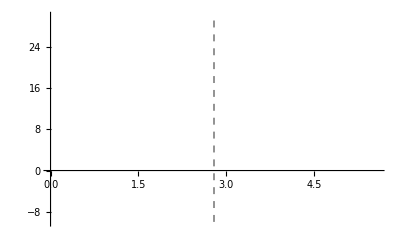

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{13.2353,13.1171,13.022,12.9428,12.8755,12.8176,12.7673,12.7235,12.6852,12.6517,12.6226,12.5973,12.5755,12.5568,12.5412,12.5283,12.518,12.5102,12.5046,12.5013,12.5,12.5008,12.5035,12.5081,12.5145,12.5227,12.5326,12.5442,12.5575,12.5725,12.5891,12.6073,12.627,12.6484,12.6714,12.6959,12.722,12.7497,12.779,12.8098,12.8423,12.8764,12.9121,12.9495,12.9885,13.0293,13.0717,13.116,13.162,13.2098,13.2595,13.3111,13.3646,13.4202,13.4778,13.5375,13.5994,13.6635,13.73,13.7988,13.8701,13.944,14.0205,14.0998,14.182,14.2672,14.3555,14.4471,14.5421,14.6407,14.7431,14.8495,14.9601,15.0751,15.1949,15.3197,15.4499,15.5858,15.7278,15.8764,16.0321,16.1955,16.3673,16.5483,16.7395,16.9417,17.1564,17.3851,17.6296,17.8922,18.1758,18.4842,18.8222,19.1966,19.6172,20.0991,20.6675,21.3712,22.3352,24.4767}

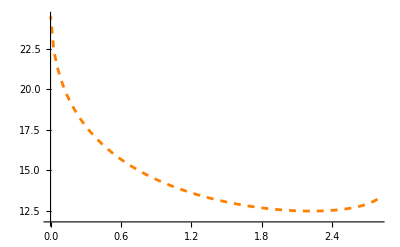

```mathematica
Solve[Eliminate[{b/d==(d+α+U f)/(β0-(n  Vk)/2),Vk== Sqrt[(U (1-f)λ)/(b/d) - (3 U (1-f)λ^2)/(8 Vk b/d)] }/.Vk->(9/16)λ/.paramsall,U],λ];
valVk = λ/.%[[2]]
limiteVk=ListPlot[{{%,-10},{%,30}}, Joined->True, PlotStyle-> Directive[Opacity[0.5,Black],Dashed, Thickness@0.003]]

A[v_]:=seq 
list1=Array[#&,100,{valVk ,0.001}];

Solve[Vk^2== (U (1-f)λ)/A[Vk] - (3 U (1-f)λ^2)/(8 Vk A[Vk]), Vk][[1]] /.seq->b/d/.paramsall;
listUcK4=Table[Re[U/.FindRoot[b/d==(d+α+U f)/(β0-(n Vk)/2)/.%/.paramsall ,{U,20}]],{λ,list1}]

pointsK4=ListPlot[Transpose[{list1,listUcK4}], PlotStyle->{Dashed, Orange}, Joined->True]
```

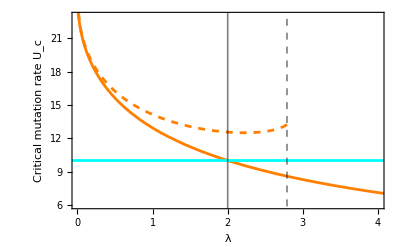

```mathematica
Show[plotucWSSM,pointsK4,plotucHC,limiteU,limiteVk, PlotRange->{{0.0080,4},{6,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["λ",13],Style["Critical mutation rate U_c",13]}]
```

```mathematica
(*Import Data*)data=Import["/Users/martin/Documents/lethal/figures/Uc_regimes/simul_deter_2025_lambda.csv","Data"];
epsilon=0.001;  (*Match your Python threshold*)

(*Separate survived/extinct populations*)
survived=Select[data,#[[3]]>epsilon&];  (*I>epsilon*)

(*Create Plot*)
dotplot=Show[ListPlot[{survived[[All,{1,2}]]},PlotStyle->{Black},PlotMarkers->{"●"},(*Hollow circles vs.filled*)ImageSize->800,Frame->True,FrameLabel->{"λ (Variance)","Critical Mutation Rate \!$$\*SubscriptBox[$$U$$, $$c$$]$$"},GridLines->Automatic,GridLinesStyle->LightGray,BaseStyle->{FontFamily->"Arial",FontSize->12}],PlotRange->{{0,3.1},{2,24}}  (*Adjust to match Python's PlotRange*)];

(*Define the grid*)UValues=Range[7,23,2];  (*U:7,9,...,23*)
LambdaValues=Range[0.001,4.001,0.5];  (*λ:0.001,0.501,...,4.001*)

(*Generate all (λ,U) grid points*)
gridPoints=Flatten[Outer[List,LambdaValues,UValues],1];

(*Create the plot*)
fakedotplot=ListPlot[gridPoints,PlotStyle->Directive[Black,Opacity[0.3]],(*Adjust marker appearance*)PlotMarkers->{"○",12},(*Hollow circles,size 12*)Frame->True,FrameLabel->{Style["λ (Variance)",13],Style["Critical Mutation Rate \!$$\*SubscriptBox[$$U$$, $$c$$]$$",13]},PlotRange->{{0,4.1},{6,24}},(*Extend slightly beyond grid*)FrameStyle->Black,ImageSize->800,BaseStyle->{FontFamily->"Arial",FontSize->12}];

Show[plotucWSSM,pointsK4,plotucHC,limiteVk,rec1,rec2,dotplot,fakedotplot, PlotRange->{{0.000,4},{6,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Mutational variance λ",20],Style["Critical mutation rate U_c",20]},FrameTicksStyle->Directive[FontSize->14]]
Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>"_lambda.pdf",%, ImageResolution->300, ImageSize->600]
```

-Graphics-

/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n2_lambda.pdf

```mathematica
pointsK4
```

-Graphics-

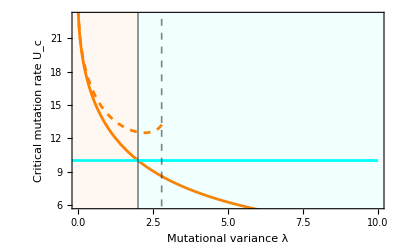

/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n2_lambdaλ.pdf

```mathematica
Show[plotucWSSM,pointsK4,plotucHC,limiteU,limiteVk,rec1,rec2, PlotRange->{{0.000,10},{6,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Mutational variance λ",20],Style["Critical mutation rate U_c",20]},FrameTicksStyle->Directive[FontSize->14]]
Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>"_lambda"<>ToString[lam]<>".pdf",%, ImageResolution->300, ImageSize->600]
```

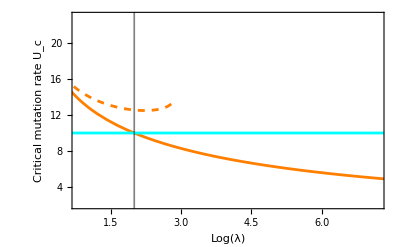

/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n2_lambdaλ.png

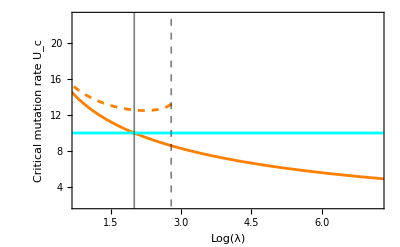

```mathematica
If[nnn==2,
aaa=Show[plotucWSSM,pointsK4,plotucHC,limiteU,limiteVk, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}];
Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>".png",Show[plotucWSSM,pointsK4,plotucHC,limiteU, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}], ImageResolution->300];
Show[plotucWSSM,pointsK4,plotucHC,limiteU, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}]]



(*If[nnn==1,
aaa=Show[limiteU,plotucWSSM,pointsK4,plotucHC,pointsHC3, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}];
Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>".png",Show[limiteU,plotucWSSM,pointsK4,plotucHC,pointsHC3, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}], ImageResolution->300];
Show[limiteU,plotucWSSM,pointsK4,plotucHC,pointsHC3, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(λ)",13],Style["Critical mutation rate U_c",13]}]
]*)

Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>"_lambda"<>ToString[lam]<>".png",aaa, ImageResolution->300]
aaa
```

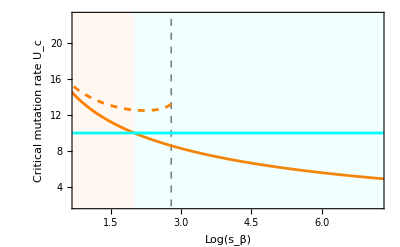

/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n2_lambdaλ.png

```mathematica
Show[limiteVk,plotucWSSM,pointsK4,plotucHC,rec1,rec2, PlotRange->{{0.80,7.2},{2,23}}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black, Black}, FrameLabel->{Style["Log(s_β)",13],Style["Critical mutation rate U_c",13]}]
Export["/Users/martin/Documents/lethal/figures/Uc_regimes/regimes_sbeta_Uc_n"<>ToString[nnn]<>"_lambda"<>ToString[lam]<>".png",%, ImageResolution->300]
```